```mathematica
base:=Show[Graphics[{
{GrayLevel[0.8],Thin,Table[{(*A*)Line[{{i/2,i*√3/2},{1-i/2,i*√3/2}}],(*S*)Line[{{i,0},{i/2,i*√3/2}}],
(*C*)Line[{{1-i,0},{1-i/2,i*√3/2}}]},{i,0,1,0.05}]},
{EdgeForm[Thick],FaceForm[None],Polygon[{{0,0},{0.5,√3/2},{1,0}}]},
Table[{
(*A*)Text[Style[i,15],{i/2,i*√3/2},{1.5,0}],
(*S*)Text[Style[1-i,15],{i,0},{-1.5,0},{1/2,-1}],
(*C*)Text[Style[1-i,15],{1-i/2,i*√3/2},{-1.5,0},{1.5,2}]
},{i,0.1,0.9,0.1}],
Text[Style["solute",17],{0.5,√3/2},{0,-1}],Text[Style["solvent  ",17],{0,0},{1,0}],
Text[Style[" carrier",17],{1,0},{-1,0}],
}],
Plot[-1.551*x^2+1.536*x,{x,0,0.99},PlotStyle->{Thick,Black}]];
```

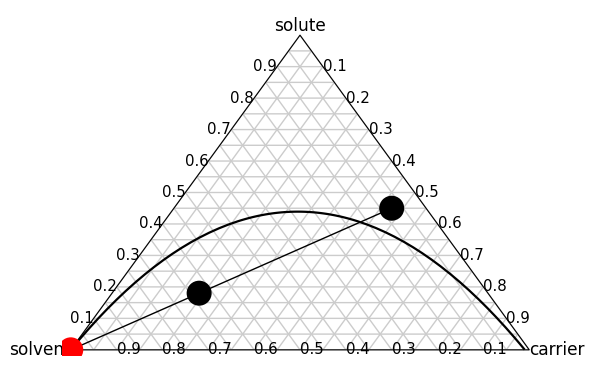
{xA→0.179995,xS→0.630003,xC→0.190003}
0.28
0.15588-Graphics-

```mathematica
Module[{F,S,M,xF,yF,sol,xM,yM},
F=1000;
S=1500;
M=F+S;

xF=0.7;yF=0.3897;

sol:=Quiet@Solve[(yF*2/√3)*F==xA*M∧(1-(xF+yF/√3))*F+S==xS*M∧xA+xS+xC==1,{xA,xS,xC}][[1]];
xM:=1-(xS/.sol)-yM/√3;
yM:=(√3/2)*xA/.sol;
Row[{
Column[{sol,xM,yM}],
Show[base,
Graphics[{
{Thick,Line[{{0,0},{xF,yF}}]},
{PointSize[0.03],Point[{xF,yF}],Red,Point[{0,0}],Black,Point[{xM,yM}]}
}],ImageSize->{600,385}]
}]
(*sol:=Quiet@Solve[{(yF*2/√3)*1000==xA*2500,(1-(xF+yF/√3))*1000+1500==xS*2500,xA+xS+xC==1},{{xA,0},{xS,0},{xC,0}}];
xM:=1-(xS/.sol)-M/√3;M:=(√3/2)*xA/.sol;*)

]
```

```mathematica
wtA[y_]:=y*2/√3;
wtS[x_,y_]:=1-(x+y/√3);
wtC[x_,y_]:=x-y/√3;
```

```mathematica
Simplify[1-(y+(1-y/√3-x)*√3/2)*2/√3]
```

x-y/(√3)